```mathematica
Quit[];
```

```mathematica
$Assumptions = β>0 && k>0 &&d>0 ;&& t≳ 0 ;
```

```mathematica
f[t_]=Piecewise[{{1,t<1},{Exp[-d],1<t<2},{Exp[-2*d],2<t<3},{Exp[-3*d],t>3}}]
```

Piecewise[{{1, t<1}, {ⅇ^-d, 1<t<2}, {ⅇ^(-2 d), 2<t<3}, {ⅇ^(-3 d), t>3}, {0, True}}]

```mathematica
q0=5000;p0=3000;k=7000;α=0.2;β=0.15;d=0.975;
```

```mathematica
q0=5;p0=3;k=30;α=8;β=2;d=0.75;
```

```mathematica
q[t_]=Simplify[q0*k*Exp[β*t]*f[t]/(k+q0*Integrate[β*Exp[β*T]*f[T],{T,0,t},Assumptions->Element[t,Reals]])]
```

(30 ⅇ^(2 t) (Piecewise[{{1, t<1}, {0.472367, 1<t<2}, {0.22313, 2<t<3}, {0.105399, t>3}, {0, True}}]))/(6+(Piecewise[{{2. ⅇ^t Sinh[t], t≤1.}, {2.89871+0.472367 ⅇ^(2. t), 1.<t≤2.}, {16.5066+0.22313 ⅇ^(2. t), 2.<t≤3.}, {64.0026+0.105399 ⅇ^(2. t), True}}]))

```mathematica
qq[t_] = Simplify[Log[q[t]]]
```

Log[(30 ⅇ^(2 t) (Piecewise[{{1, t<1}, {0.472367, 1<t<2}, {0.22313, 2<t<3}, {0.105399, t>3}, {0, True}}]))/(6+(Piecewise[{{2. ⅇ^t Sinh[t], t≤1.}, {2.89871+0.472367 ⅇ^(2. t), 1.<t≤2.}, {16.5066+0.22313 ⅇ^(2. t), 2.<t≤3.}, {64.0026+0.105399 ⅇ^(2. t), True}}]))]

```mathematica
sol = DSolve[{w'[t]==-α*w[t]+ α*qq[t],w[0]==Log[p0]},w[t],t]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{w[t]→Piecewise[{{-0.25 ⅇ^(-8. t) (1.18053+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.2 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[(30. ⅇ^(2. t))/(5.+1. ⅇ^(2 t))]), t≤1}, {-0.25 ⅇ^(-8. t) (-9830.7-13.6048 ⅇ^(8. t)+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.0530826 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[ⅇ^(2. t)/(18.8386+1. ⅇ^(2. t))]), 1<t≤2}, {-0.25 ⅇ^(-8. t) (-3.01477×10^7-13.6048 ⅇ^(8. t)+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.00991401 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[ⅇ^(2. t)/(100.867+1. ⅇ^(2. t))]), 2<t≤3}, {-0.25 ⅇ^(-8. t) (-9.09021×10^10-13.6048 ⅇ^(8. t)+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.00150565 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[ⅇ^(2. t)/(664.166+1. ⅇ^(2. t))]), True}}]}}

```mathematica
p[t_] =Exp[w[t]]/.sol
```

{ⅇ^Piecewise[{{-0.25 ⅇ^(-8. t) (1.18053+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.2 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[(30. ⅇ^(2. t))/(5.+1. ⅇ^(2 t))]), t≤1}, {-0.25 ⅇ^(-8. t) (-9830.7-13.6048 ⅇ^(8. t)+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.0530826 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[ⅇ^(2. t)/(18.8386+1. ⅇ^(2. t))]), 1<t≤2}, {-0.25 ⅇ^(-8. t) (-3.01477×10^7-13.6048 ⅇ^(8. t)+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.00991401 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[ⅇ^(2. t)/(100.867+1. ⅇ^(2. t))]), 2<t≤3}, {-0.25 ⅇ^(-8. t) (-9.09021×10^10-13.6048 ⅇ^(8. t)+1. ⅇ^(8. t) Hypergeometric2F1[1.,4.,5.,-0.00150565 ⅇ^(2. t)]-4. ⅇ^(8. t) Log[ⅇ^(2. t)/(664.166+1. ⅇ^(2. t))]), True}}]}

```mathematica
p[0]
```

{3.}

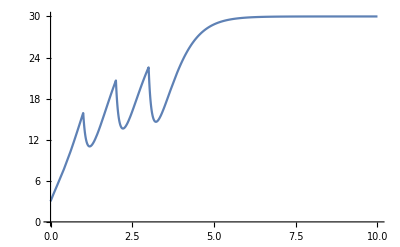

```mathematica
p1 = Plot[p[t],{t,0,10}]
```

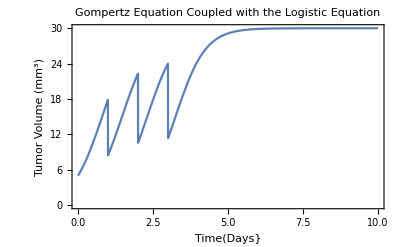

```mathematica
p2 =Plot[q[t],{t,0,10},PlotRange->{0,30},PlotLabel->"Gompertz Equation Coupled with the Logistic Equation",ExclusionsStyle->Dashed,Frame->{True,True,False,False},FrameLabel->{"Time(Days}","Tumor Volume (mm^3)"}]
```

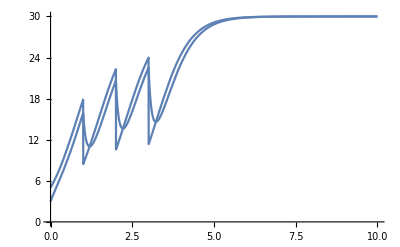

```mathematica
Show[{p1,p2}]
```